```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/insertion.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

4910.04-0.488735 words+0.0000110122 words^2

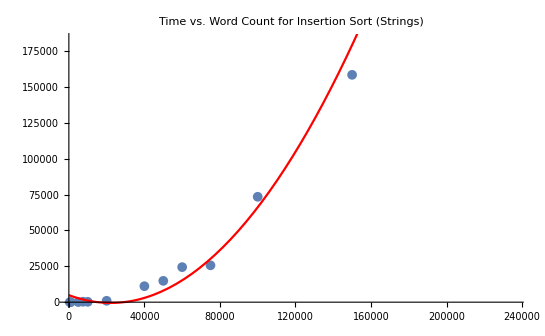

Set::write: Tag List in {248746, 25155950, 1796449531, 1332153645, 99935231, 1031956336, 398825791, 62650, 6244551, 623612400, 901267906, 14186214, 1406502306}[words_] is Protected.

1.99876×10^8+6674.14 words

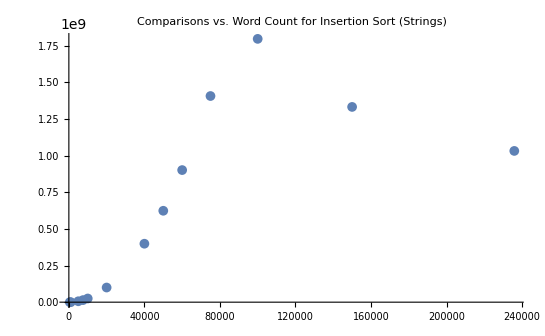

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Insertion Sort (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Insertion Sort (Strings)"]
```